## Ticks

```mathematica
<<MaTeX`
LTicks[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,NumberForm[x,{1,1}],{0.02,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];

STicks[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,"",{0.02,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];
LTicksLog[emin_,emax_,step1_,step2_]:=Flatten[{Table[{Log[10^i],Superscript[10,i],{0.02,0},Thickness[0.004]},{i,emin,emax,step1}],{{Log[1],1,{0.02,0},Thickness[0.004]}},Flatten[Table[{Log[j*10^i], ,{0.01,0},Thickness[0.002]},{i,emin,emax,step1},{j,step2,9,step2}],1]},1];STicksLog[emin_,emax_,step1_,step2_]:=Flatten[{Table[{Log[10^i],,{0.02,0},Thickness[0.004]},{i,emin,emax,step1}],Flatten[Table[{Log[j*10^i], ,{0.01,0},Thickness[0.002]},{i,emin,emax,step1},{j,step2,9,step2}],1],{{Log[1],,{0.02,0},Thickness[0.004]}}},1];
```

## Long-time behaviour for several p’s

### Functions

```mathematica
F1Plus[x_,y_]:=1/x^2(Cosh[x]+x/y Sinh[x]-1);
F1Minus[x_,y_]:=F1Plus[y,x];
F1Total[x_,y_,p_]:=p F1Plus[x,y]+(1-p)F1Minus[x,y];G0[s_,r1_,r2_,k_]:=((s+r1)(s+r2))/(r1(s+r2)+s(s+r2)Cosh[k Sqrt[s+r1]]+s Sqrt[(s+r1)]Sqrt[(s+r2)]Sinh[k Sqrt[s+r1]]) 
G0Inverse[s_,r1_,r2_]:=FullSimplify[1/G0[s,r1,r2,1]];PoleFunction[s_,r1_,r2_]:=r1(s+r2)+s(s+r2)Cosh[Sqrt[s+r1]]+s Sqrt[(s+r1)]Sqrt[(s+r2)]Sinh[Sqrt[s+r1]];
```

### p=0

```mathematica
Clear[PDF000]
```

```mathematica
folder="0";SetDirectory["/Users/gregarval/projects/Disordered resetting/Results_Paper/p=" <> folder];
files=FileNames["*.dat"]; var={};
For[i=1,i<=Length[files],i++,var=AppendTo[var,Import[TextString["Results_"] <> ToString[i] <> ".dat"][[1]]]]; var=Flatten[var,1];
```

```mathematica
PDF000=var;width=0.1;
```

```mathematica
{bins,counts}=HistogramList[PDF000,{0,10,width}];
```

```mathematica
Parameters=Import["Optimal_1.txt","List"];
```

```mathematica
p=Parameters[[1]];nruns=Parameters[[2]]*Length[files];
```

```mathematica
LaplFunction1[s_]:=G0[s,r1,r2,1];LaplFunction2[s_]:=G0[s,r2,r1,1];
```

```mathematica
Limit[G0Inverse[s,r1var,r2var],{r1var->0,r2var->∞}]
```

Cosh[√s]

```mathematica
Polp0=s/.FindRoot[Cosh[Sqrt[s]]==0,{s,0}];
```

```mathematica
width=0.1;xm=0;xM=10;ΔxM=2;Δxm=1;SizeLegend=1.5;eps=10^-4;MarkerSize=12;
PlotAbsorbingLogp000=Show[ListLogPlot[Transpose@{Most[bins]+width/2,counts/nruns/width},PlotMarkers->Style["○",Black,Thick,MarkerSize]],LogPlot[InverseLaplaceTransform[1/Cosh[Sqrt[s]],s,N@t],{t,eps,10+eps},PlotRange->All,PlotStyle->{Dashed,Red}],LogPlot[1/SeriesCoefficient[Cosh[Sqrt[s]],{s,Polp0,1}] Exp[Polp0 t],{t,0,xM},PlotRange->All,PlotStyle->{RGBColor[0.880722, 0.611041, 0.142051],DotDashed,Thick}],PlotRange->{{0,xM},{Log[10^-4],Log[2]}},Frame-> True,FrameLabel->{MaTeX["t",Magnification->2],MaTeX["f(t|0)",Magnification->2]},Axes->None,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameTicks->{{LTicksLog[-4,-1,1,1],STicksLog[-4,-1,1,1]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},ImageSize->Large,AspectRatio->0.6,PlotRangePadding->None];
```

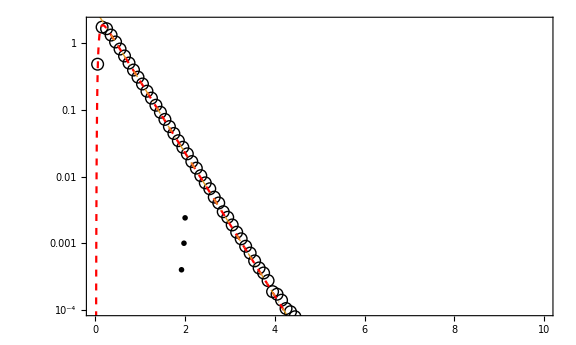

```mathematica
SizeLegend=2;LeftAlign=2;VerticalAlign=4 10^-4;
PlotFinalp0=Show[PlotAbsorbingLogp000,Epilog-> {Inset[MaTeX["p = 0",Magnification->SizeLegend],{LeftAlign,Log[VerticalAlign+5 VerticalAlign]},{Center,Center}],Inset[MaTeX["\\alpha_+ = \\infty",Magnification->SizeLegend],{LeftAlign-0.025,Log[VerticalAlign+1.5 VerticalAlign]},{Center,Center}],Inset[MaTeX["\\alpha_- = 0",Magnification->SizeLegend],{LeftAlign-0.08,Log[VerticalAlign]},{Center,Center}]}]
```

```mathematica
PlotPanel1=Show[ListLogPlot[Transpose@{Most[bins]+width/2,counts/nruns/width},PlotMarkers->Style["○",Black,Thick,MarkerSize]],LogPlot[InverseLaplaceTransform[1/Cosh[Sqrt[s]],s,N@t],{t,eps,10+eps},PlotRange->All,PlotStyle->{Dashed,Red}],LogPlot[1/SeriesCoefficient[Cosh[Sqrt[s]],{s,Polp0,1}] Exp[Polp0 t],{t,0,xM},PlotRange->All,PlotStyle->{RGBColor[0.880722, 0.611041, 0.142051],DotDashed,Thick}],PlotRange->{{0,xM},{Log[10^-4],Log[2]}},Frame-> True,Axes->None,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameTicks->{{LTicksLog[-4,-1,1,1],STicksLog[-4,-1,1,1]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},ImageSize->Large,ImagePadding->{{40,10},{25,1}},AspectRatio->0.6,PlotRangePadding->None,FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}}];
```

```mathematica
SizeLegend=2;LeftAlign=2;VerticalAlign=4 10^-4;
PlotPanel1v2=Show[PlotPanel1,Epilog-> {Inset[MaTeX["p = 0",Magnification->SizeLegend],{LeftAlign,Log[VerticalAlign+5 VerticalAlign]},{Center,Center}],Inset[MaTeX["\\alpha_+ = \\infty",Magnification->SizeLegend],{LeftAlign-0.025,Log[VerticalAlign+1.5 VerticalAlign]},{Center,Center}],Inset[MaTeX["\\alpha_- = 0",Magnification->SizeLegend],{LeftAlign-0.08,Log[VerticalAlign]},{Center,Center}]}];
```

### p=0,05

```mathematica
Clear[PDF005]
```

```mathematica
folder="0,05";SetDirectory["/Users/gregarval/projects/Disordered resetting/Results_Paper/p=" <> folder];
files=FileNames["*.dat"]; var={};
For[i=1,i<=Length[files],i++,var=AppendTo[var,Import[TextString["Results_"] <> ToString[i] <> ".dat"][[1]]]]; var=Flatten[var,1];
```

```mathematica
Evaluate[Symbol["PDF0"<>StringTake[folder,-2]]]=var;
```

```mathematica
{bins,counts}=HistogramList[PDF005,{0,10,width}];
```

```mathematica
Parameters=Import["Optimal_1.txt","List"];
```

```mathematica
r1=Parameters[[1]];r2=Parameters[[2]];p=Parameters[[3]];nruns=Parameters[[4]]*Length[files];
```

```mathematica
Pol1=s/.FindRoot[G0Inverse[s,r1,r2]==0,{s,0}];
Pol2=s/.FindRoot[G0Inverse[s,r2,r1]==0,{s,0}];
Res1=Series[G0Inverse[s,r1,r2],{s,Pol1,3}];
Res2=Series[G0Inverse[s,r2,r1],{s,Pol2,3}];
```

```mathematica
LaplFunction1[s_]:=G0[s,r1,r2,1];LaplFunction2[s_]:=G0[s,r2,r1,1];PoleL=Max[Pol1,Pol2];PoleM=Min[Pol1,Pol2];
```

```mathematica
max=10;width=0.1;xm=0;xM=max;ym=0;yM=1;ΔxM=2;Δxm=1;ΔyM=0.2;Δym=0.1;
eps=10^-3;PlotAbsorbing=Show[ListPlot[Transpose@{Most[bins]+width/2,counts/nruns/width},PlotRange->{{0,max},{0,1}},PlotMarkers->Style["○",Black,Thick,12]],Plot[(p (Pol1+r1)(Pol1+r2))/SeriesCoefficient[PoleFunction[s,r1,r2],{s,Pol1,1}] Exp[Pol1 t]+((1-p)(Pol2+r1)(Pol2+r2))/SeriesCoefficient[PoleFunction[s,r2,r1],{s,Pol2,1}] Exp[Pol2 t],{t,0,8}],Plot[InverseLaplaceTransform[p LaplFunction1[s]+(1-p)LaplFunction2[s],s,N@t],{t,eps,10+eps},PlotRange->All,PlotStyle->{Dashed,Red}],PlotRange->{{0,6},{0,1}},Frame-> True,FrameLabel->{MaTeX["t",Magnification->2],MaTeX["f(t|0)",Magnification->2]},FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameTicks->{{LTicks[ym,yM,ΔyM,Δym],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},ImageSize->Large,AspectRatio->0.6];
```

```mathematica
max=10;width=0.1;xm=0;xM=max;ym=0;yM=1;ΔxM=2;Δxm=1;ΔyM=0.2;Δym=0.1;MarkerSize=12;
PlotAbsorbingLogp005=Show[ListLogPlot[Transpose@{Most[bins]+width/2,counts/nruns/width},PlotMarkers->Style["○",Black,Thick,MarkerSize]],LogPlot[(p (Pol1+r1)(Pol1+r2))/SeriesCoefficient[PoleFunction[s,r1,r2],{s,Pol1,1}] Exp[Pol1 t]+((1-p)(Pol2+r1)(Pol2+r2))/SeriesCoefficient[PoleFunction[s,r2,r1],{s,Pol2,1}] Exp[Pol2 t],{t,0,10},PlotRange->All],LogPlot[InverseLaplaceTransform[p LaplFunction1[s]+(1-p)LaplFunction2[s],s,N@t],{t,eps,10+eps},PlotRange->All,PlotStyle->{Dashed,Red}],LogPlot[{p(PoleL+r1)(PoleL+r2)/SeriesCoefficient[PoleFunction[s,r1,r2],{s,PoleL,1}]Exp[PoleL t],(1-p)(PoleM+r1)(PoleM+r2)/SeriesCoefficient[PoleFunction[s,r2,r1],{s,PoleM,1}]Exp[PoleM t],p(PoleL+r1)(PoleL+r2)/SeriesCoefficient[PoleFunction[s,r1,r2],{s,PoleL,1}]Exp[PoleL t]+(1-p)(PoleM+r1)(PoleM+r2)/SeriesCoefficient[PoleFunction[s,r2,r1],{s,PoleM,1}]Exp[PoleM t]},{t,0,20},PlotStyle->{Dotted,DotDashed,StandardForm}],PlotRange->{{0,10},{Log[10^-4],Log[2]}},Frame-> True,FrameLabel->{MaTeX["t",Magnification->2],MaTeX["f(t|0)",Magnification->2]},Axes->None,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameTicks->{{LTicksLog[-4,-1,1,1],STicksLog[-4,-1,1,1]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},ImageSize->Large,AspectRatio->0.6,PlotRangePadding->None];
```

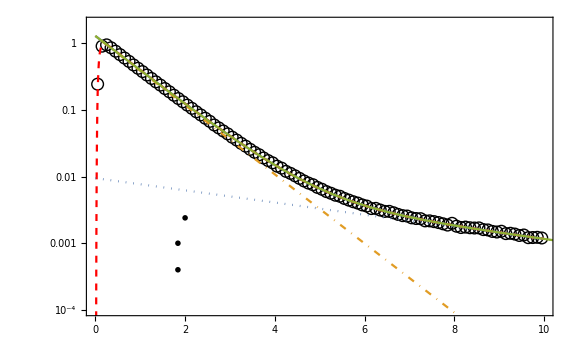

```mathematica
SizeLegend=2;LeftAlign=2;VerticalAlign=4 10^-4;
PlotFinalp005=Show[PlotAbsorbingLogp005,Epilog-> {Inset[MaTeX["p = 0.05",Magnification->SizeLegend],{LeftAlign,Log[VerticalAlign+5 VerticalAlign]},{Center,Center}],Inset[MaTeX["\\alpha_+ = 2.88",Magnification->SizeLegend],{LeftAlign-0.16,Log[VerticalAlign+1.5 VerticalAlign]},{Center,Center}],Inset[MaTeX["\\alpha_- = 0.91",Magnification->SizeLegend],{LeftAlign-0.16,Log[VerticalAlign]},{Center,Center}]}]
```

```mathematica
PlotPanel2=Show[ListLogPlot[Transpose@{Most[bins]+width/2,counts/nruns/width},PlotMarkers->Style["○",Black,Thick,MarkerSize]],LogPlot[(p (Pol1+r1)(Pol1+r2))/SeriesCoefficient[PoleFunction[s,r1,r2],{s,Pol1,1}] Exp[Pol1 t]+((1-p)(Pol2+r1)(Pol2+r2))/SeriesCoefficient[PoleFunction[s,r2,r1],{s,Pol2,1}] Exp[Pol2 t],{t,0,10},PlotRange->All],LogPlot[InverseLaplaceTransform[p LaplFunction1[s]+(1-p)LaplFunction2[s],s,N@t],{t,eps,10+eps},PlotRange->All,PlotStyle->{Dashed,Red}],LogPlot[{p(PoleL+r1)(PoleL+r2)/SeriesCoefficient[PoleFunction[s,r1,r2],{s,PoleL,1}]Exp[PoleL t],(1-p)(PoleM+r1)(PoleM+r2)/SeriesCoefficient[PoleFunction[s,r2,r1],{s,PoleM,1}]Exp[PoleM t],p(PoleL+r1)(PoleL+r2)/SeriesCoefficient[PoleFunction[s,r1,r2],{s,PoleL,1}]Exp[PoleL t]+(1-p)(PoleM+r1)(PoleM+r2)/SeriesCoefficient[PoleFunction[s,r2,r1],{s,PoleM,1}]Exp[PoleM t]},{t,0,20},PlotStyle->{Dotted,DotDashed,StandardForm}],PlotRange->{{0,10},{Log[10^-4],Log[2]}},Frame-> True,Axes->None,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameTicks->{{LTicksLog[-4,-1,1,1],STicksLog[-4,-1,1,1]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},ImageSize->Large,AspectRatio->0.6,FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},PlotRangePadding->None,ImagePadding->{{40,10},{25,1}}];
```

```mathematica
SizeLegend=2;LeftAlign=2;VerticalAlign=4 10^-4;
PlotPanel2v2=Show[PlotPanel2,Epilog-> {Inset[MaTeX["p = 0.05",Magnification->SizeLegend],{LeftAlign,Log[VerticalAlign+5 VerticalAlign]},{Center,Center}],Inset[MaTeX["\\alpha_+ = 2.88",Magnification->SizeLegend],{LeftAlign-0.16,Log[VerticalAlign+1.5 VerticalAlign]},{Center,Center}],Inset[MaTeX["\\alpha_- = 0.91",Magnification->SizeLegend],{LeftAlign-0.16,Log[VerticalAlign]},{Center,Center}]}];
```

#### Short times - Inset

Checking

```mathematica
{binsShortTime,countsShortTime}=HistogramList[PDF005,{0.01,1,0.01}];
```

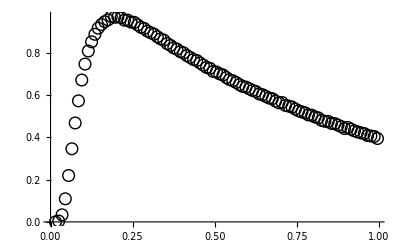

```mathematica
ListPlot[Transpose@{Most[binsShortTime]+0.01/2,countsShortTime/nruns/0.01},PlotMarkers->Style["○",Black,Thick,12]]
```

Using uniformly spaced ticks in logarithmic space

#### Using logarithmic equidistant spaces

```mathematica
<<MaTeX`
LTicks[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,NumberForm[x,{1,1}],{0.04,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.02,0},Thickness[0.002]},{x,xm,xM,Δxm}]];

STicks[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,"",{0.04,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.02,0},Thickness[0.002]},{x,xm,xM,Δxm}]];
LTicksLog[emin_,emax_,step1_,step2_]:=Flatten[{Table[{Log[10^i],Superscript[10,i],{0.04,0},Thickness[0.004]},{i,emin,emax,step1}],{{Log[1],1,{0.04,0},Thickness[0.004]}},Flatten[Table[{Log[j*10^i],"" ,{0.02,0},Thickness[0.002]},{i,emin,emax,step1},{j,step2,9,step2}],1]},1];  
STicksLog[emin_,emax_,step1_,step2_]:=Flatten[{Table[{Log[10^i],,{0.04,0},Thickness[0.004]},{i,emin,emax,step1}],{{Log[1],,{0.04,0},Thickness[0.004]}},Flatten[Table[{Log[j*10^i],"" ,{0.02,0},Thickness[0.002]},{i,emin,emax,step1},{j,step2,9,step2}],1]},1]; 

LTicksLog2[emin_,emax_,step1_,step2_]:=Flatten[{Table[{10^i,Superscript[10,i],{0.04,0},Thickness[0.004]},{i,emin,emax,step1}],Table[{10^i,"" ,{0.02,0},Thickness[0.002]},{i,emin,emax,step2}]},1];STicksLog2[emin_,emax_,step1_,step2_]:=Flatten[{Table[{10^i,,{0.04,0},Thickness[0.004]},{i,emin,emax,step1}],Table[{10^i,"" ,{0.02,0},Thickness[0.002]},{i,emin,emax,step2}]},1];
```

```mathematica
{binsLog,countsLog}=HistogramList[PDF005,{PowerRange[0.001,1,(1/0.001)^(1/100)]}];
```

```mathematica
MarkerSize=12;CountsPlot=ListLogLogPlot[Transpose@{Most[binsLog]+(Differences[binsLog])/2,countsLog/nruns/(Differences[binsLog])},PlotMarkers->Style["○",Black,Thick,MarkerSize]];
```

```mathematica
InversePlot=LogLogPlot[InverseLaplaceTransform[p LaplFunction1[s]+(1-p)LaplFunction2[s],s,N@t],{t,0.01,1+eps},PlotRange->All,PlotStyle->{Dashed,Red}];
```

```mathematica
ExpansionPlot=LogLogPlot[{p(PoleL+r1)(PoleL+r2)/SeriesCoefficient[PoleFunction[s,r1,r2],{s,PoleL,1}]Exp[PoleL t]+(1-p)(PoleM+r1)(PoleM+r2)/SeriesCoefficient[PoleFunction[s,r2,r1],{s,PoleM,1}]Exp[PoleM t]},{t,0.1,1},PlotRange->All,PlotStyle->RGBColor[0.560181, 0.691569, 0.194885]];
```

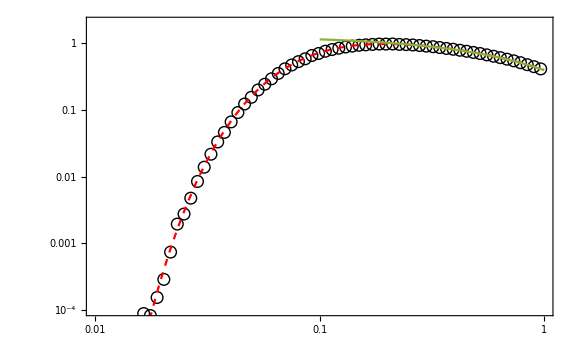

```mathematica
InsetPlot=Show[CountsPlot,InversePlot,ExpansionPlot,PlotRange->{{Log[10^-2],Log[10^0]},{Log[10^-4],Log[2]}},Frame-> True,FrameLabel->{MaTeX["t",Magnification->2],MaTeX["f(t|0)",Magnification->2]},Axes->None,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameTicks->{{LTicksLog[-4,-1,1,1],STicksLog[-4,-1,1,1]},{LTicksLog[-2,-1,1,1],STicksLog[-2,-1,1,1]}},ImageSize->Large,AspectRatio->0.6,PlotRangePadding->None]
```

### p=0,3

```mathematica
Clear[var]
```

```mathematica
folder="0,3";SetDirectory["/Users/gregarval/projects/Disordered resetting/Results_Paper/p=" <> folder];
files=FileNames["*.dat"]; var={};
For[i=1,i<=Length[files],i++,var=AppendTo[var,Import[TextString["Results_"] <> ToString[i] <> ".dat"][[1]]]]; var=Flatten[var,1];
```

```mathematica
Evaluate[Symbol["PDF0"<>StringTake[folder,-1]]]=var;
```

```mathematica
{bins,counts}=HistogramList[PDF03,{0,10,width}];
```

```mathematica
Parameters=Import["Optimal_1.txt","List"];
```

```mathematica
r1=Parameters[[1]];r2=Parameters[[2]];p=Parameters[[3]];nruns=Parameters[[4]]*Length[files];
```

```mathematica
Pol1=s/.FindRoot[G0Inverse[s,r1,r2]==0,{s,0}];
Pol2=s/.FindRoot[G0Inverse[s,r2,r1]==0,{s,0}];
Res1=Series[G0Inverse[s,r1,r2],{s,Pol1,3}];
Res2=Series[G0Inverse[s,r2,r1],{s,Pol2,3}];
```

```mathematica
LaplFunction1[s_]:=G0[s,r1,r2,1];LaplFunction2[s_]:=G0[s,r2,r1,1];PoleL=Max[Pol1,Pol2];PoleM=Min[Pol1,Pol2];
```

```mathematica
max=10;width=0.1;xm=0;xM=max;ym=0;yM=1;ΔxM=2;Δxm=1;ΔyM=0.2;Δym=0.1;
eps=10^-3;PlotAbsorbing=Show[ListPlot[Transpose@{Most[bins]+width/2,counts/nruns/width},PlotRange->{{0,max},{0,1}},PlotMarkers->Style["○",Black,Thick,12]],Plot[(p (Pol1+r1)(Pol1+r2))/SeriesCoefficient[PoleFunction[s,r1,r2],{s,Pol1,1}] Exp[Pol1 t]+((1-p)(Pol2+r1)(Pol2+r2))/SeriesCoefficient[PoleFunction[s,r2,r1],{s,Pol2,1}] Exp[Pol2 t],{t,0,8}],Plot[InverseLaplaceTransform[p LaplFunction1[s]+(1-p)LaplFunction2[s],s,N@t],{t,eps,10+eps},PlotRange->All,PlotStyle->{Dashed,Red}],PlotRange->{{0,6},{0,1}},Frame-> True,FrameLabel->{MaTeX["t",Magnification->2],MaTeX["f(t;x_0)",Magnification->2]},FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameTicks->{{LTicks[ym,yM,ΔyM,Δym],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},ImageSize->Large,AspectRatio->0.6];
```

```mathematica
max=10;width=0.1;xm=0;xM=max;ym=0;yM=1;ΔxM=2;Δxm=1;ΔyM=0.2;Δym=0.1;MarkerSize=12;
PlotAbsorbingLog03=Show[ListLogPlot[Transpose@{Most[bins]+width/2,counts/nruns/width},PlotMarkers->Style["○",Black,Thick,MarkerSize]],LogPlot[(p (Pol1+r1)(Pol1+r2))/SeriesCoefficient[PoleFunction[s,r1,r2],{s,Pol1,1}] Exp[Pol1 t]+((1-p)(Pol2+r1)(Pol2+r2))/SeriesCoefficient[PoleFunction[s,r2,r1],{s,Pol2,1}] Exp[Pol2 t],{t,0,10},PlotRange->All],LogPlot[InverseLaplaceTransform[p LaplFunction1[s]+(1-p)LaplFunction2[s],s,N@t],{t,eps,10+eps},PlotRange->All,PlotStyle->{Dashed,Red}],LogPlot[{p(PoleL+r1)(PoleL+r2)/SeriesCoefficient[PoleFunction[s,r1,r2],{s,PoleL,1}]Exp[PoleL t],(1-p)(PoleM+r1)(PoleM+r2)/SeriesCoefficient[PoleFunction[s,r2,r1],{s,PoleM,1}]Exp[PoleM t],p(PoleL+r1)(PoleL+r2)/SeriesCoefficient[PoleFunction[s,r1,r2],{s,PoleL,1}]Exp[PoleL t]+(1-p)(PoleM+r1)(PoleM+r2)/SeriesCoefficient[PoleFunction[s,r2,r1],{s,PoleM,1}]Exp[PoleM t]},{t,0,20},PlotStyle->{Dotted,DotDashed,StandardForm}],PlotRange->{{0,10},{Log[10^-4],Log[2]}},Frame-> True,FrameLabel->{MaTeX["t",Magnification->2],MaTeX["f(t|0)",Magnification->2]},Axes->None,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameTicks->{{LTicksLog[-4,-1,1,1],STicksLog[-4,-1,1,1]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},ImageSize->Large,AspectRatio->0.6,PlotRangePadding->None];
```

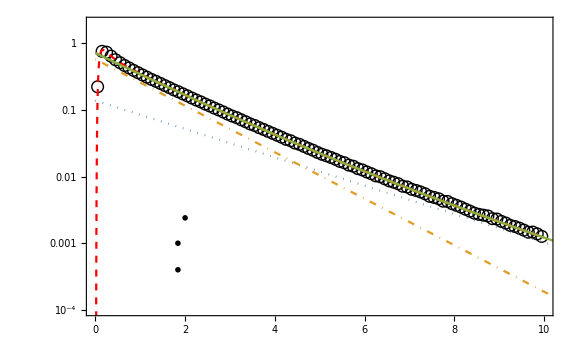

```mathematica
SizeLegend=2;LeftAlign=2;VerticalAlign=4 10^-4;
PlotFinalp03=Show[PlotAbsorbingLog03,Epilog-> {Inset[MaTeX["p = 0.30",Magnification->SizeLegend],{LeftAlign,Log[VerticalAlign+5 VerticalAlign]},{Center,Center}],Inset[MaTeX["\\alpha_+ = 1.90",Magnification->SizeLegend],{LeftAlign-0.16,Log[VerticalAlign+1.5 VerticalAlign]},{Center,Center}],Inset[MaTeX["\\alpha_- = 1.34",Magnification->SizeLegend],{LeftAlign-0.16,Log[VerticalAlign]},{Center,Center}]}]
```

```mathematica
max=10;width=0.1;xm=0;xM=max;ym=0;yM=1;ΔxM=2;Δxm=1;ΔyM=0.2;Δym=0.1;MarkerSize=12;
PlotPanel3=Show[ListLogPlot[Transpose@{Most[bins]+width/2,counts/nruns/width},PlotMarkers->Style["○",Black,Thick,MarkerSize]],LogPlot[(p (Pol1+r1)(Pol1+r2))/SeriesCoefficient[PoleFunction[s,r1,r2],{s,Pol1,1}] Exp[Pol1 t]+((1-p)(Pol2+r1)(Pol2+r2))/SeriesCoefficient[PoleFunction[s,r2,r1],{s,Pol2,1}] Exp[Pol2 t],{t,0,10},PlotRange->All],LogPlot[InverseLaplaceTransform[p LaplFunction1[s]+(1-p)LaplFunction2[s],s,N@t],{t,eps,10+eps},PlotRange->All,PlotStyle->{Dashed,Red}],LogPlot[{p(PoleL+r1)(PoleL+r2)/SeriesCoefficient[PoleFunction[s,r1,r2],{s,PoleL,1}]Exp[PoleL t],(1-p)(PoleM+r1)(PoleM+r2)/SeriesCoefficient[PoleFunction[s,r2,r1],{s,PoleM,1}]Exp[PoleM t],p(PoleL+r1)(PoleL+r2)/SeriesCoefficient[PoleFunction[s,r1,r2],{s,PoleL,1}]Exp[PoleL t]+(1-p)(PoleM+r1)(PoleM+r2)/SeriesCoefficient[PoleFunction[s,r2,r1],{s,PoleM,1}]Exp[PoleM t]},{t,0,20},PlotStyle->{Dotted,DotDashed,StandardForm}],PlotRange->{{0,10},{Log[10^-4],Log[2]}},Frame-> True,Axes->None,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameTicks->{{LTicksLog[-4,-1,1,1],STicksLog[-4,-1,1,1]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},ImageSize->Large,AspectRatio->0.6,PlotRangePadding->None,ImagePadding->{{40,10},{25,1}}];
```

```mathematica
SizeLegend=2;LeftAlign=2;VerticalAlign=4 10^-4;
PlotPanel3v2=Show[PlotPanel3,Epilog-> {Inset[MaTeX["p = 0.30",Magnification->SizeLegend],{LeftAlign,Log[VerticalAlign+5 VerticalAlign]},{Center,Center}],Inset[MaTeX["\\alpha_+ = 1.90",Magnification->SizeLegend],{LeftAlign-0.16,Log[VerticalAlign+1.5 VerticalAlign]},{Center,Center}],Inset[MaTeX["\\alpha_- = 1.34",Magnification->SizeLegend],{LeftAlign-0.16,Log[VerticalAlign]},{Center,Center}]}];
```

### p=0,5

```mathematica
Clear[PDF05]
```

```mathematica
Clear[var]
```

```mathematica
folder="0,5";SetDirectory["/Users/gregarval/projects/Disordered resetting/Results_Paper/p=" <> folder];
files=FileNames["*.dat"]; var={};
For[i=1,i<=Length[files],i++,var=AppendTo[var,Import[TextString["Results_"] <> ToString[i] <> ".dat"][[1]]]]; var=Flatten[var,1];
```

```mathematica
Evaluate[Symbol["PDF0"<>StringTake[folder,-1]]]=var;
```

```mathematica
{bins,counts}=HistogramList[PDF05,{0,10,width}];
```

```mathematica
Parameters=Import["Optimal_1.txt","List"];
```

```mathematica
r1=Parameters[[1]];r2=Parameters[[2]];p=Parameters[[3]];nruns=Parameters[[4]]*Length[files];
```

```mathematica
Pol1=s/.FindRoot[G0Inverse[s,r1,r2]==0,{s,0}];
Pol2=s/.FindRoot[G0Inverse[s,r2,r1]==0,{s,0}];
Res1=Series[G0Inverse[s,r1,r2],{s,Pol1,3}];
Res2=Series[G0Inverse[s,r2,r1],{s,Pol2,3}];
```

```mathematica
LaplFunction1[s_]:=G0[s,r1,r2,1];LaplFunction2[s_]:=G0[s,r2,r1,1];PoleL=Max[Pol1,Pol2];PoleM=Min[Pol1,Pol2];
```

```mathematica
max=10;width=0.1;xm=0;xM=max;ym=0;yM=1;ΔxM=2;Δxm=1;ΔyM=0.2;Δym=0.1;
eps=10^-3;PlotAbsorbing=Show[ListPlot[Transpose@{Most[bins]+width/2,counts/nruns/width},PlotRange->{{0,max},{0,1}},PlotMarkers->Style["○",Black,Thick,12]],Plot[(p (Pol1+r1)(Pol1+r2))/SeriesCoefficient[PoleFunction[s,r1,r2],{s,Pol1,1}] Exp[Pol1 t]+((1-p)(Pol2+r1)(Pol2+r2))/SeriesCoefficient[PoleFunction[s,r2,r1],{s,Pol2,1}] Exp[Pol2 t],{t,0,8}],Plot[InverseLaplaceTransform[p LaplFunction1[s]+(1-p)LaplFunction2[s],s,N@t],{t,eps,10+eps},PlotRange->All,PlotStyle->{Dashed,Red}],PlotRange->{{0,6},{0,1}},Frame-> True,FrameLabel->{MaTeX["t",Magnification->2],MaTeX["f(t;x_0)",Magnification->2]},FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameTicks->{{LTicks[ym,yM,ΔyM,Δym],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},ImageSize->Large,AspectRatio->0.6];
```

```mathematica
max=10;width=0.1;xm=0;xM=max;ym=0;yM=1;ΔxM=2;Δxm=1;ΔyM=0.2;Δym=0.1;MarkerSize=12;
PlotAbsorbingLog05=Show[ListLogPlot[Transpose@{Most[bins]+width/2,counts/nruns/width},PlotMarkers->Style["○",Black,Thick,MarkerSize]],LogPlot[(p (Pol1+r1)(Pol1+r2))/SeriesCoefficient[PoleFunction[s,r1,r2],{s,Pol1,1}] Exp[Pol1 t]+((1-p)(Pol2+r1)(Pol2+r2))/SeriesCoefficient[PoleFunction[s,r2,r1],{s,Pol2,1}] Exp[Pol2 t],{t,0,10},PlotRange->All],LogPlot[InverseLaplaceTransform[p LaplFunction1[s]+(1-p)LaplFunction2[s],s,N@t],{t,eps,10+eps},PlotRange->All,PlotStyle->{Dashed,Red}],LogPlot[{p(PoleL+r1)(PoleL+r2)/SeriesCoefficient[PoleFunction[s,r1,r2],{s,PoleL,1}]Exp[PoleL t],(1-p)(PoleM+r1)(PoleM+r2)/SeriesCoefficient[PoleFunction[s,r2,r1],{s,PoleM,1}]Exp[PoleM t],p(PoleL+r1)(PoleL+r2)/SeriesCoefficient[PoleFunction[s,r1,r2],{s,PoleL,1}]Exp[PoleL t]+(1-p)(PoleM+r1)(PoleM+r2)/SeriesCoefficient[PoleFunction[s,r2,r1],{s,PoleM,1}]Exp[PoleM t]},{t,0,20},PlotStyle->{Dotted,DotDashed,StandardForm}],PlotRange->{{0,10},{Log[10^-4],Log[2]}},Frame-> True,FrameLabel->{MaTeX["t",Magnification->2],MaTeX["f(t|0)",Magnification->2]},Axes->None,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameTicks->{{LTicksLog[-4,-1,1,1],STicksLog[-4,-1,1,1]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},ImageSize->Large,AspectRatio->0.6,PlotRangePadding->None];
```

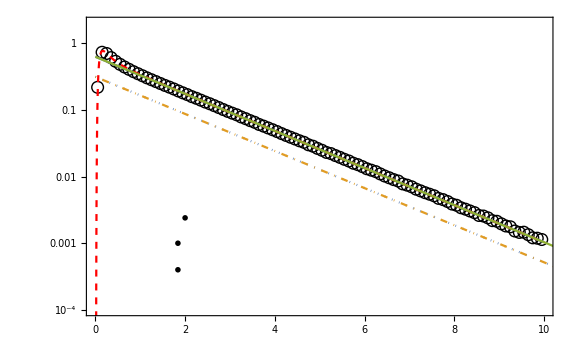

```mathematica
SizeLegend=2;LeftAlign=2;VerticalAlign=4 10^-4;
PlotFinalp05=Show[PlotAbsorbingLog05,Epilog-> {Inset[MaTeX["p = 0.50",Magnification->SizeLegend],{LeftAlign,Log[VerticalAlign+5 VerticalAlign]},{Center,Center}],Inset[MaTeX["\\alpha_+ = 1.59",Magnification->SizeLegend],{LeftAlign-0.16,Log[VerticalAlign+1.5 VerticalAlign]},{Center,Center}],Inset[MaTeX["\\alpha_- = 1.59",Magnification->SizeLegend],{LeftAlign-0.16,Log[VerticalAlign]},{Center,Center}]}]
```

```mathematica
max=10;width=0.1;xm=0;xM=max;ym=0;yM=1;ΔxM=2;Δxm=1;ΔyM=0.2;Δym=0.1;MarkerSize=12;
PlotPanel4=Show[ListLogPlot[Transpose@{Most[bins]+width/2,counts/nruns/width},PlotMarkers->Style["○",Black,Thick,MarkerSize]],LogPlot[(p (Pol1+r1)(Pol1+r2))/SeriesCoefficient[PoleFunction[s,r1,r2],{s,Pol1,1}] Exp[Pol1 t]+((1-p)(Pol2+r1)(Pol2+r2))/SeriesCoefficient[PoleFunction[s,r2,r1],{s,Pol2,1}] Exp[Pol2 t],{t,0,10},PlotRange->All],LogPlot[InverseLaplaceTransform[p LaplFunction1[s]+(1-p)LaplFunction2[s],s,N@t],{t,eps,10+eps},PlotRange->All,PlotStyle->{Dashed,Red}],LogPlot[{p(PoleL+r1)(PoleL+r2)/SeriesCoefficient[PoleFunction[s,r1,r2],{s,PoleL,1}]Exp[PoleL t],(1-p)(PoleM+r1)(PoleM+r2)/SeriesCoefficient[PoleFunction[s,r2,r1],{s,PoleM,1}]Exp[PoleM t],p(PoleL+r1)(PoleL+r2)/SeriesCoefficient[PoleFunction[s,r1,r2],{s,PoleL,1}]Exp[PoleL t]+(1-p)(PoleM+r1)(PoleM+r2)/SeriesCoefficient[PoleFunction[s,r2,r1],{s,PoleM,1}]Exp[PoleM t]},{t,0,20},PlotStyle->{Dotted,DotDashed,StandardForm}],PlotRange->{{0,10},{Log[10^-4],Log[2]}},Frame-> True,Axes->None,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameTicks->{{LTicksLog[-4,-1,1,1],STicksLog[-4,-1,1,1]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},ImageSize->Large,AspectRatio->0.6,PlotRangePadding->None,FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Automatic},{Automatic,Automatic}},ImagePadding->{{40,10},{25,1}}];
```

```mathematica
SizeLegend=2;LeftAlign=2;VerticalAlign=4 10^-4;
PlotPanel4v2=Show[PlotPanel4,Epilog-> {Inset[MaTeX["p = 0.50",Magnification->SizeLegend],{LeftAlign,Log[VerticalAlign+5 VerticalAlign]},{Center,Center}],Inset[MaTeX["\\alpha_+ = 1.59",Magnification->SizeLegend],{LeftAlign-0.16,Log[VerticalAlign+1.5 VerticalAlign]},{Center,Center}],Inset[MaTeX["\\alpha_- = 1.59",Magnification->SizeLegend],{LeftAlign-0.16,Log[VerticalAlign]},{Center,Center}]}];
```

## Saving individual plots

```mathematica
Export["/Users/gregarval/Documents/LongTimeBehaviour_p=0.png",PlotFinalp0,ImageResolution->1000]
```

/Users/gregarval/Documents/LongTimeBehaviour_p=0.png

```mathematica
Export["/Users/gregarval/Documents/LongTimeBehaviour_p=0_3.png",PlotFinalp03,ImageResolution->1000]
```

/Users/gregarval/Documents/LongTimeBehaviour_p=0_3.png

```mathematica
Export["/Users/gregarval/Documents/LongTimeBehaviour_p=0_5.png",PlotFinalp05,ImageResolution->1000]
```

/Users/gregarval/Documents/LongTimeBehaviour_p=0_5.png

```mathematica
Export["/Users/gregarval/Documents/LongTimeBehaviour_p=0_05.png",PlotFinalp005,ImageResolution->1000]
```

/Users/gregarval/Documents/LongTimeBehaviour_p=0_05.png

```mathematica
Export["/Users/gregarval/Documents/Inset_ShortTimeBehaviour_p=0_05.png",InsetPlot,ImageResolution->1000]
```

/Users/gregarval/Documents/Inset_ShortTimeBehaviour_p=0_05.png

## Figure 1

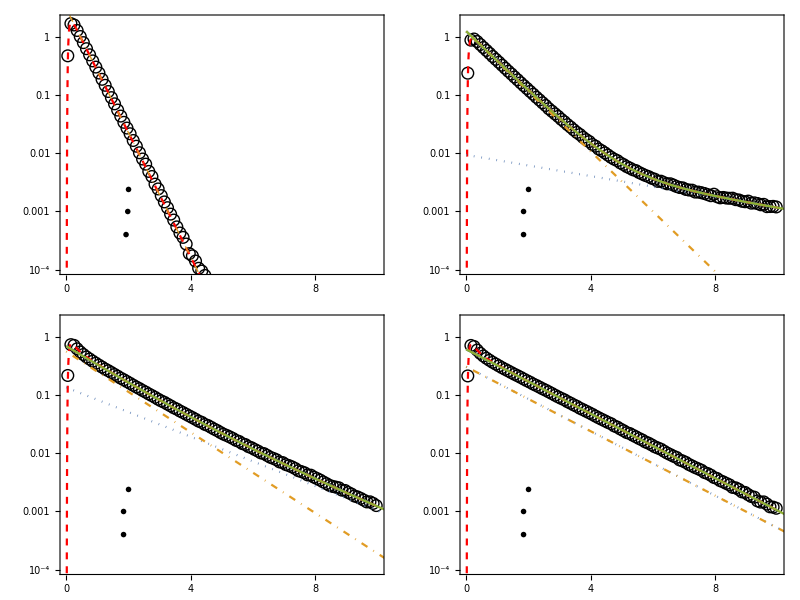

```mathematica
Grid[{{PlotFinalp0,PlotFinalp005},{PlotFinalp03,PlotFinalp05}},Spacings->{0,0}]
```

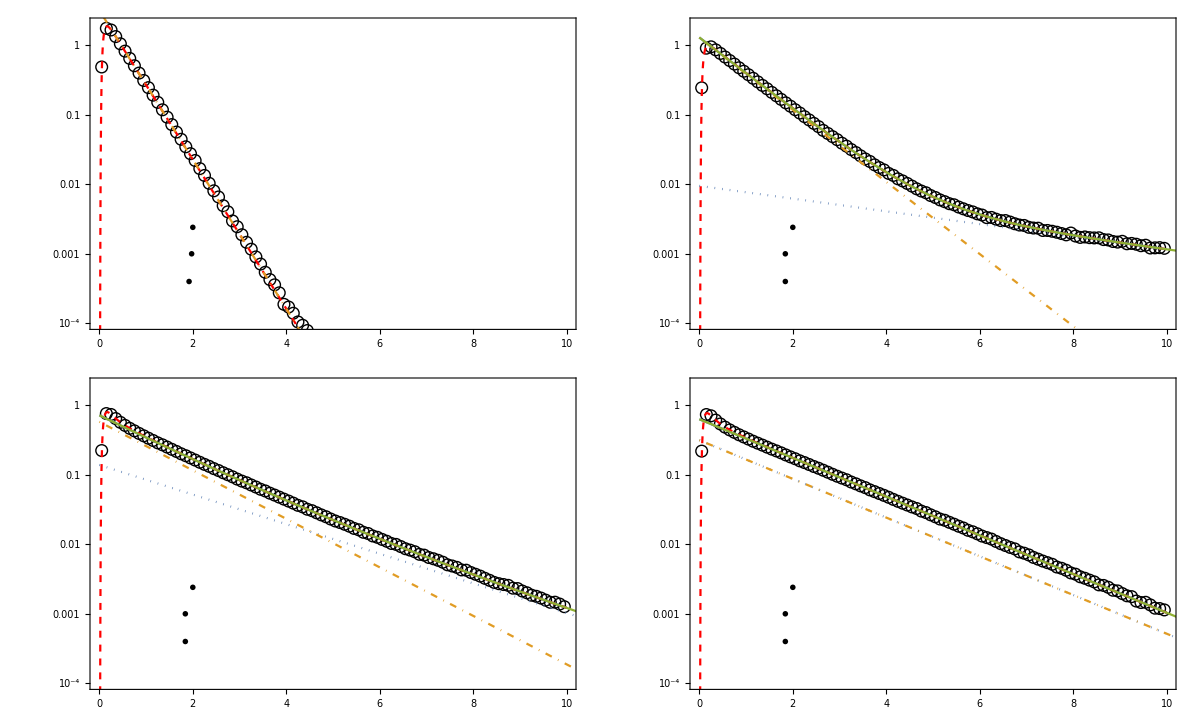
-Graphics--Graphics--Graphics-

```mathematica
LabelSize=3;PlotAllPanels=Labeled[GraphicsGrid[{{PlotPanel1v2,PlotPanel2v2},{PlotPanel3v2,PlotPanel4v2}},Spacings->{0,0},ImageSize->1200],{MaTeX["t",Magnification->LabelSize],MaTeX["f(t|0)",Magnification->LabelSize]},{Bottom,Left},RotateLabel->True,LabelStyle->Directive[Bold,FontFamily->"Consolas",FontSize->16]

]
```

```mathematica
Export["/Users/gregarval/Documents/LongTimeBehaviour_SeveralPs.png",PlotAllPanels,ImageResolution->800]
```

/Users/gregarval/Documents/LongTimeBehaviour_SeveralPs.png

## Appendix B

```mathematica
G0[s_,r1_,r2_,k_]:=((s+r1)(s+r2))/(r1(s+r2)+s(s+r2)Cosh[k Sqrt[s+r1]]+s Sqrt[(s+r1)]Sqrt[(s+r2)]Sinh[k Sqrt[s+r1]])
G0Inverse[s_,r1_,r2_]:=FullSimplify[1/G0[s,r1,r2,1]]
PoleFunction[s_,r1_,r2_]:=r1(s+r2)+s(s+r2)Cosh[Sqrt[s+r1]]+s Sqrt[(s+r1)]Sqrt[(s+r2)]Sinh[Sqrt[s+r1]]
```

```mathematica
<<MaTeX`
LTicks[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,NumberForm[x,{2,1}],{0.02,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];

STicks[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,"",{0.02,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];
```

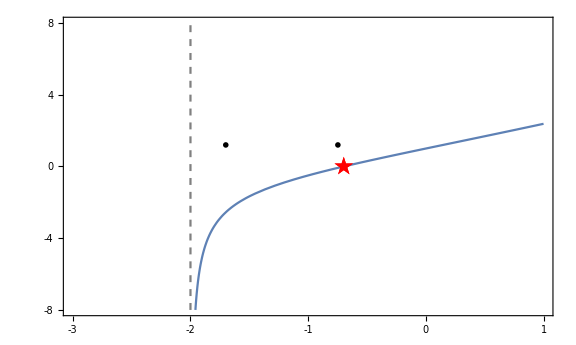

```mathematica
ar1=1;ar2=2;xm=-ar2-1;xM=1;ym=-8;yM=8;ΔxM=1;Δxm=0.5;ΔyM=4;Δym=2;sstar=s/.FindRoot[G0Inverse[s,ar1,ar2],{s,0.5}];
AppendixC=Show[Plot[G0Inverse[s,ar1,ar2],{s,xm,xM},PlotRange->{{xm,xM},{ym,yM}},Frame-> True,FrameLabel->{MaTeX["s",Magnification->2],MaTeX["\\phi_+^{-1}(s|0)",Magnification->2]},FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],AxesStyle->Directive[Black,10,FontFamily->"Times New Roman",Thickness[0.001]],Method->{"AxesInFront"->False},FrameTicks->{{LTicks[ym,yM,ΔyM,Δym],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},ImageSize->Large,AspectRatio->0.6,PlotRangePadding->None],ListPlot[{{sstar,0}},PlotMarkers->Style["★",Red,20]],ParametricPlot[{-ar2,x},{x,ym,yM},PlotStyle->{Dashed,Gray}],Epilog-> {Inset[MaTeX["s_+^*",Magnification->1.5],{sstar-0.05,1.2}],,Inset[MaTeX["s=-\\alpha_-^2",Magnification->1.5],{-ar2+0.3,1.2}]},ImagePadding->{{70,5},{60,10}}]
```